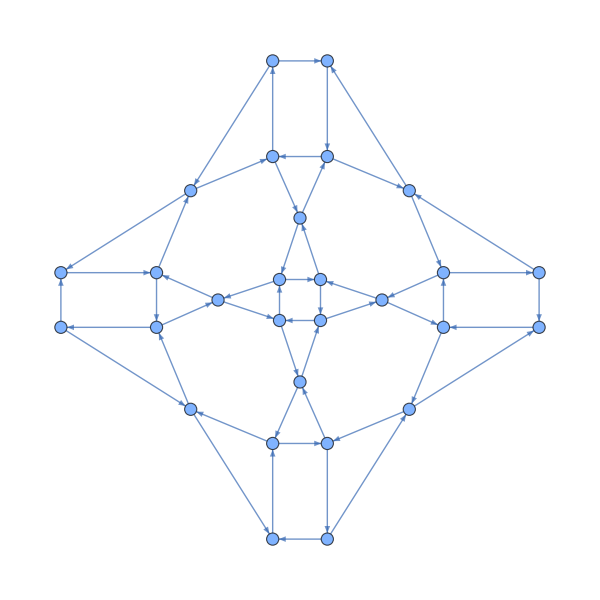

```mathematica
g=Graph[{"2"->"7","2"->"1","29"->"21","29"->"36","28"->"29","28"->"16","21"->"28","21"->"17","20"->"28","20"->"15","16"->"20","16"->"9","9"->"5","9"->"21","17"->"22","17"->"9","36"->"33","36"->"32","33"->"29","33"->"34","27"->"26","27"->"20","15"->"27","15"->"8","32"->"27","32"->"35","26"->"32","26"->"14","35"->"36","35"->"31","34"->"35","34"->"30","31"->"34","31"->"25","24"->"31","24"->"12","30"->"23","30"->"33","22"->"30","22"->"10","10"->"11","10"->"17","5"->"1","5"->"16","4"->"5","4"->"3","8"->"4","8"->"14","14"->"15","14"->"19","19"->"26","19"->"13","25"->"19","25"->"24","13"->"25","13"->"7","12"->"13","12"->"18","18"->"24","18"->"11","23"->"18","23"->"22","11"->"23","11"->"6","6"->"10","6"->"2","1"->"6","1"->"4","3"->"8","3"->"2","7"->"3","7"->"12"},EdgeStyle->Arrowheads[0.02]];
coords=GraphEmbedding[IGLayoutTutte[UndirectedGraph[g],OuterFace->{"1","2","3","4"}]];
g = Graph[g,VertexCoordinates->coords];VertexDelete[g,ToString /@ Range[1,8], ImageSize->{600,600}](*36 pieces*)
```

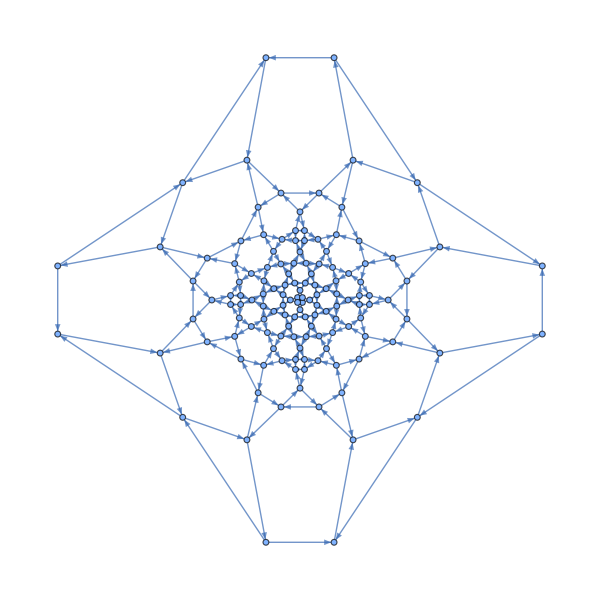

```mathematica
g = Graph[{"2"->"3","2"->"6","140"->"134","140"->"144","1"->"2","1"->"5","4"->"1","4"->"8","3"->"4","3"->"7","7"->"2","7"->"13","8"->"3","8"->"15","5"->"4","5"->"9","6"->"1","6"->"11","12"->"7","12"->"24","10"->"6","10"->"22","16"->"5","16"->"28","14"->"8","14"->"26","15"->"20","15"->"14","20"->"16","20"->"27","9"->"17","9"->"16","17"->"10","17"->"21","11"->"18","11"->"10","18"->"23","18"->"12","13"->"19","13"->"12","19"->"14","19"->"25","27"->"15","27"->"43","28"->"20","28"->"36","21"->"9","21"->"37","22"->"17","22"->"30","23"->"11","23"->"39","24"->"18","24"->"32","25"->"13","25"->"41","26"->"19","26"->"34","35"->"27","35"->"48","34"->"35","34"->"42","42"->"26","42"->"66","33"->"25","33"->"47","48"->"34","48"->"55","43"->"35","43"->"60","29"->"45","29"->"21","44"->"28","44"->"68","36"->"44","36"->"29","60"->"44","60"->"67","68"->"60","68"->"76","67"->"43","67"->"91","75"->"67","75"->"83","55"->"75","55"->"54","54"->"48","54"->"82","82"->"74","82"->"83","83"->"55","83"->"96","91"->"75","91"->"100","45"->"36","45"->"49","37"->"29","37"->"57","38"->"22","38"->"62","30"->"38","30"->"31","31"->"46","31"->"23","39"->"31","39"->"58","40"->"64","40"->"24","32"->"40","32"->"33","47"->"32","47"->"53","41"->"33","41"->"59","59"->"42","59"->"65","66"->"59","66"->"74","74"->"90","74"->"54","96"->"82","96"->"115","115"->"114","115"->"107","56"->"45","56"->"84","76"->"56","76"->"92","49"->"56","49"->"69","92"->"68","92"->"108","100"->"92","100"->"107","107"->"91","107"->"123","114"->"96","114"->"122","90"->"66","90"->"106","99"->"90","99"->"105","89"->"99","89"->"73","105"->"89","105"->"121","65"->"41","65"->"89","73"->"65","73"->"81","53"->"73","53"->"52","81"->"53","81"->"95","52"->"47","52"->"80","72"->"52","72"->"88","58"->"40","58"->"63","64"->"58","64"->"72","88"->"64","88"->"104","80"->"72","80"->"81","95"->"80","95"->"113","113"->"112","113"->"105","112"->"95","112"->"120","104"->"112","104"->"98","98"->"88","98"->"103","87"->"98","87"->"71","63"->"39","63"->"87","71"->"63","71"->"79","103"->"87","103"->"119","120"->"104","120"->"132","121"->"113","121"->"127","106"->"99","106"->"114","122"->"106","122"->"134","127"->"122","127"->"133","134"->"127","134"->"135","123"->"115","123"->"128","135"->"123","135"->"140","128"->"135","128"->"124","108"->"100","108"->"116","124"->"108","124"->"136","116"->"93","116"->"124","84"->"77","84"->"76","93"->"84","93"->"109","77"->"49","77"->"93","69"->"61","69"->"77","61"->"37","61"->"85","57"->"38","57"->"61","62"->"57","62"->"70","46"->"30","46"->"51","51"->"50","51"->"71","50"->"46","50"->"78","70"->"50","70"->"86","86"->"62","86"->"102","78"->"70","78"->"79","79"->"51","79"->"94","94"->"78","94"->"111","111"->"110","111"->"103","110"->"94","110"->"118","102"->"110","102"->"97","97"->"86","97"->"101","85"->"97","85"->"69","101"->"85","101"->"117","109"->"101","109"->"116","117"->"109","117"->"125","118"->"130","118"->"102","125"->"118","125"->"129","130"->"125","130"->"131","119"->"111","119"->"126","126"->"131","126"->"120","131"->"119","131"->"138","138"->"130","138"->"142","132"->"126","132"->"133","133"->"121","133"->"139","139"->"132","139"->"143","142"->"139","142"->"141","141"->"138","141"->"144","137"->"136","137"->"141","129"->"137","129"->"117","136"->"129","136"->"128","143"->"140","143"->"142","144"->"143","144"->"137"},VertexSize->1.2,EdgeStyle->Arrowheads[0.01]];
coords = GraphEmbedding[IGLayoutTutte[UndirectedGraph[g], "OuterFace"->{"1","2", "3", "4"}]];
g = Graph[g, VertexCoordinates->coords];
g = VertexDelete[g, ToString /@ Range[1,8], ImageSize->{600,600}]
(*144 pieces*)
```

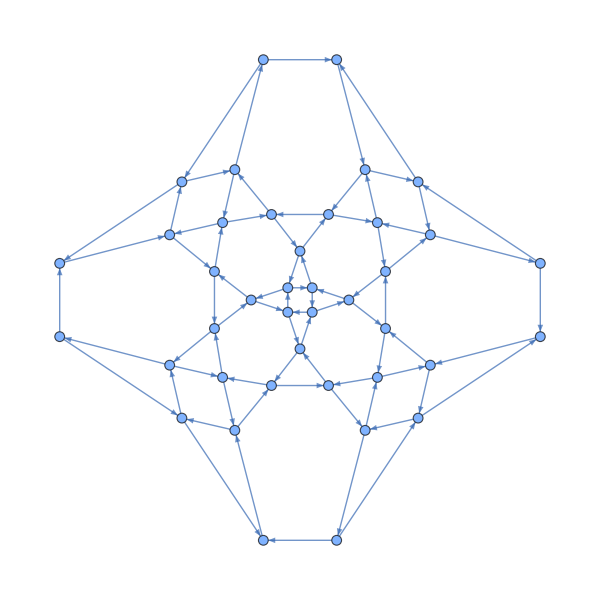

```mathematica
g = Graph[{"2"->"7","2"->"1","1"->"4","1"->"6","4"->"3","4"->"5","3"->"8","3"->"2","20"->"15","20"->"28","28"->"32","28"->"16","32"->"27","32"->"40","27"->"20","27"->"39","22"->"29","22"->"10","29"->"21","29"->"34","21"->"17","21"->"33","17"->"22","17"->"9","48"->"44","48"->"45","45"->"41","45"->"46","46"->"42","46"->"47","47"->"48","47"->"43","30"->"36","30"->"23","23"->"35","23"->"18","18"->"11","18"->"24","24"->"12","24"->"30","31"->"38","31"->"25","25"->"37","25"->"19","19"->"13","19"->"26","26"->"14","26"->"31","43"->"37","43"->"46","36"->"24","36"->"43","37"->"31","37"->"36","38"->"26","38"->"44","44"->"47","44"->"39","39"->"38","39"->"32","15"->"27","15"->"8","14"->"15","14"->"19","8"->"14","8"->"4","13"->"25","13"->"7","12"->"13","12"->"18","7"->"12","7"->"3","6"->"10","6"->"2","11"->"23","11"->"6","10"->"11","10"->"17","5"->"1","5"->"16","16"->"9","16"->"20","9"->"5","9"->"21","40"->"28","40"->"41","41"->"33","41"->"48","33"->"40","33"->"29","42"->"45","42"->"35","35"->"34","35"->"30","34"->"42","34"->"22"}, VertexSize->1,EdgeStyle->Arrowheads[0.02]]; 
coords=GraphEmbedding[IGLayoutTutte[UndirectedGraph[g],OuterFace->{"1","2","3","4"}]];
g = Graph[g,VertexCoordinates->coords];
VertexDelete[g, ToString /@ Range[1,8], ImageSize->{600,600},VertexSize->0.4]
(*48 pieces*)
```

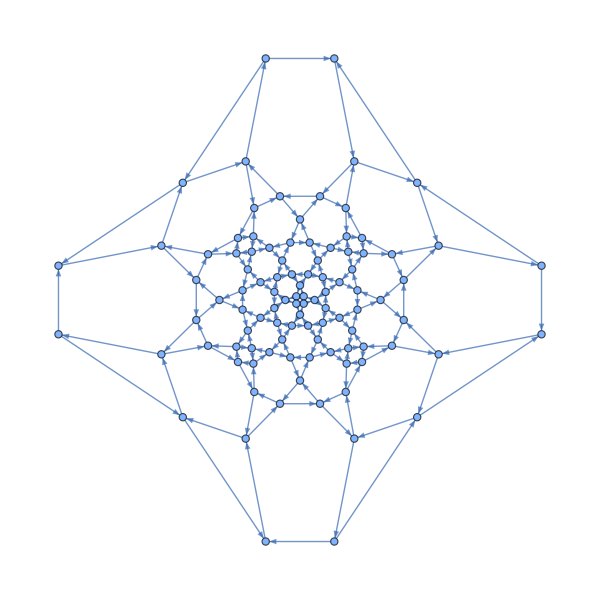

```mathematica
g = Graph[{"2"->"1","2"->"7","1"->"4","1"->"6","4"->"5","4"->"3","3"->"2","3"->"8","70"->"55","70"->"76","55"->"75","55"->"50","50"->"39","50"->"56","56"->"70","56"->"40","108"->"105","108"->"104","105"->"101","105"->"106","106"->"102","106"->"107","107"->"103","107"->"108","52"->"60","52"->"43","60"->"44","60"->"72","72"->"80","72"->"59","59"->"79","59"->"52","49"->"37","49"->"54","54"->"38","54"->"69","69"->"74","69"->"53","53"->"73","53"->"49","51"->"58","51"->"41","58"->"71","58"->"42","71"->"57","71"->"78","57"->"77","57"->"51","104"->"107","104"->"99","101"->"108","101"->"93","102"->"105","102"->"95","103"->"106","103"->"97","76"->"84","76"->"56","40"->"32","40"->"50","39"->"55","39"->"23","75"->"70","75"->"63","7"->"12","7"->"3","8"->"14","8"->"4","5"->"16","5"->"1","6"->"10","6"->"2","43"->"59","43"->"27","79"->"72","79"->"67","80"->"60","80"->"88","44"->"52","44"->"36","42"->"34","42"->"51","78"->"58","78"->"86","77"->"71","77"->"65","41"->"57","41"->"25","74"->"82","74"->"54","73"->"69","73"->"61","37"->"21","37"->"53","38"->"49","38"->"30","33"->"41","33"->"32","25"->"19","25"->"33","13"->"25","13"->"7","19"->"26","19"->"13","14"->"19","14"->"15","26"->"14","26"->"42","34"->"26","34"->"48","35"->"34","35"->"43","48"->"35","48"->"66","67"->"48","67"->"87","66"->"67","66"->"78","86"->"66","86"->"91","98"->"86","98"->"104","91"->"98","91"->"85","97"->"91","97"->"96","85"->"97","85"->"77","65"->"85","65"->"47","64"->"65","64"->"76","47"->"64","47"->"33","32"->"47","32"->"24","24"->"40","24"->"12","18"->"24","18"->"11","12"->"18","12"->"13","23"->"18","23"->"31","11"->"23","11"->"6","10"->"11","10"->"17","22"->"10","22"->"38","17"->"22","17"->"9","21"->"17","21"->"29","9"->"5","9"->"21","16"->"20","16"->"9","28"->"44","28"->"16","36"->"28","36"->"45","20"->"28","20"->"15","15"->"27","15"->"8","27"->"35","27"->"20","87"->"79","87"->"99","92"->"87","92"->"100","99"->"92","99"->"98","88"->"92","88"->"68","100"->"88","100"->"101","93"->"100","93"->"89","81"->"93","81"->"73","89"->"81","89"->"94","82"->"89","82"->"62","62"->"63","62"->"74","46"->"62","46"->"31","30"->"46","30"->"22","31"->"30","31"->"39","94"->"102","94"->"82","95"->"94","95"->"90","83"->"95","83"->"75","90"->"83","90"->"96","84"->"90","84"->"64","96"->"84","96"->"103","63"->"83","63"->"46","61"->"81","61"->"45","29"->"36","29"->"37","45"->"29","45"->"68","68"->"80","68"->"61"}, VertexSize->1,EdgeStyle->Arrowheads[0.01]];
coords = GraphEmbedding[IGLayoutTutte[UndirectedGraph[g], OuterFace-> {"1","2","3","4"}]];
g = Graph[g, VertexCoordinates->coords];
VertexDelete[g, ToString /@ Range[1,8], ImageSize->{600,600}]
(*108 pieces*)
```

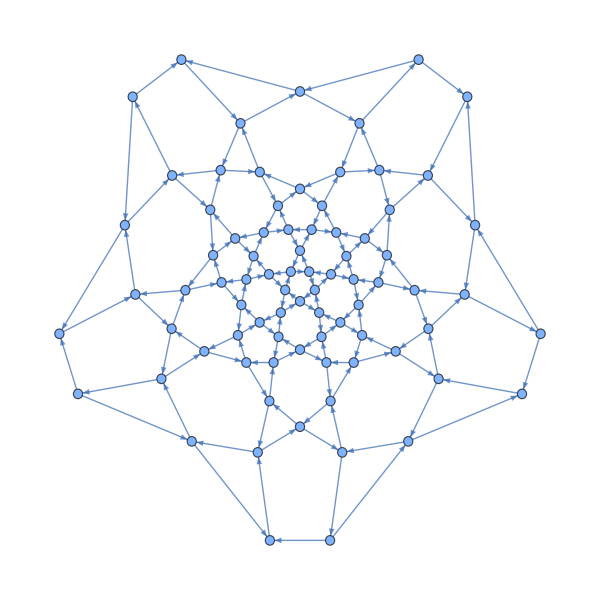

```mathematica
g = Graph[{"7"->"3","7"->"13","14"->"7","14"->"29","13"->"14","13"->"22","2"->"7","2"->"1","3"->"2","3"->"8","6"->"2","6"->"11","1"->"6","1"->"5","12"->"6","12"->"27","22"->"12","22"->"28","28"->"13","28"->"43","37"->"28","37"->"44","23"->"14","23"->"30","27"->"22","27"->"36","42"->"27","42"->"57","36"->"26","36"->"42","11"->"21","11"->"12","26"->"11","26"->"41","41"->"51","41"->"36","21"->"20","21"->"26","52"->"42","52"->"58","4"->"3","4"->"9","8"->"4","8"->"15","5"->"4","5"->"10","9"->"5","9"->"17","10"->"1","10"->"19","20"->"10","20"->"35","35"->"21","35"->"40","50"->"35","50"->"65","19"->"25","19"->"20","34"->"19","34"->"49","25"->"34","25"->"18","40"->"34","40"->"50","49"->"55","49"->"40","51"->"50","51"->"56","56"->"41","56"->"71","66"->"72","66"->"56","71"->"66","71"->"80","57"->"66","57"->"52","72"->"57","72"->"82","43"->"52","43"->"37","58"->"43","58"->"73","73"->"67","73"->"72","44"->"59","44"->"29","29"->"37","29"->"23","15"->"23","15"->"16","30"->"15","30"->"45","38"->"30","38"->"46","45"->"38","45"->"53","53"->"60","53"->"44","60"->"45","60"->"75","59"->"53","59"->"67","67"->"74","67"->"58","74"->"59","74"->"83","75"->"74","75"->"68","83"->"75","83"->"87","88"->"83","88"->"89","87"->"88","87"->"82","82"->"73","82"->"86","86"->"87","86"->"81","90"->"86","90"->"85","81"->"90","81"->"71","80"->"81","80"->"65","65"->"70","65"->"51","70"->"80","70"->"64","79"->"70","79"->"78","85"->"79","85"->"89","78"->"85","78"->"63","89"->"90","89"->"84","84"->"77","84"->"88","76"->"84","76"->"61","68"->"76","68"->"60","61"->"68","61"->"54","46"->"61","46"->"31","31"->"38","31"->"24","54"->"62","54"->"46","77"->"76","77"->"69","69"->"62","69"->"78","63"->"69","63"->"55","64"->"79","64"->"49","55"->"64","55"->"48","48"->"63","48"->"33","39"->"48","39"->"32","62"->"77","62"->"47","47"->"39","47"->"54","32"->"47","32"->"17","24"->"32","24"->"16","16"->"31","16"->"8","33"->"25","33"->"39","18"->"33","18"->"9","17"->"18","17"->"24"}, VertexSize->0.5,EdgeStyle->Arrowheads[0.02]]; 
coords = GraphEmbedding[IGLayoutTutte[UndirectedGraph[g], OuterFace->{"1","2","3","4","5"}]];
g = Graph[g, VertexCoordinates->coords];
VertexDelete[g, ToString /@ Range[1,10], ImageSize->{600,600}]
(*90 pieces*)
```

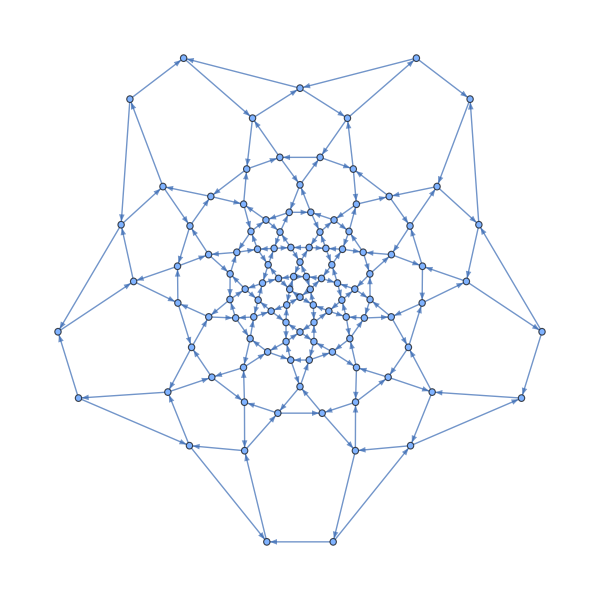

```mathematica
g = Graph[{"3"->"8","3"->"2","7"->"3","7"->"13","2"->"7","2"->"1","14"->"7","14"->"29","13"->"14","13"->"22","4"->"3","4"->"9","8"->"4","8"->"15","6"->"11","6"->"2","1"->"6","1"->"5","5"->"10","5"->"4","9"->"5","9"->"17","18"->"9","18"->"33","17"->"18","17"->"24","10"->"19","10"->"1","12"->"6","12"->"27","22"->"12","22"->"28","11"->"12","11"->"21","27"->"38","27"->"22","28"->"13","28"->"40","23"->"14","23"->"30","29"->"23","29"->"42","15"->"23","15"->"16","30"->"15","30"->"44","16"->"8","16"->"31","41"->"59","41"->"28","40"->"41","40"->"39","42"->"41","42"->"43","59"->"42","59"->"71","43"->"29","43"->"60","44"->"43","44"->"45","60"->"44","60"->"73","45"->"30","45"->"61","46"->"45","46"->"47","61"->"46","61"->"75","31"->"46","31"->"24","24"->"16","24"->"32","47"->"62","47"->"31","48"->"47","48"->"49","32"->"48","32"->"17","49"->"32","49"->"63","20"->"10","20"->"35","19"->"25","19"->"20","34"->"19","34"->"52","25"->"34","25"->"18","33"->"25","33"->"50","21"->"20","21"->"26","26"->"11","26"->"36","35"->"21","35"->"54","55"->"35","55"->"56","54"->"55","54"->"53","53"->"65","53"->"34","52"->"53","52"->"51","64"->"52","64"->"81","51"->"64","51"->"33","50"->"51","50"->"49","63"->"79","63"->"50","80"->"63","80"->"93","79"->"80","79"->"78","62"->"77","62"->"48","78"->"62","78"->"92","77"->"78","77"->"76","76"->"91","76"->"61","75"->"76","75"->"74","90"->"75","90"->"105","74"->"90","74"->"60","73"->"74","73"->"72","89"->"73","89"->"97","72"->"89","72"->"59","71"->"72","71"->"70","39"->"58","39"->"27","58"->"69","58"->"40","70"->"58","70"->"88","88"->"71","88"->"103","97"->"88","97"->"104","104"->"89","104"->"113","105"->"104","105"->"98","98"->"90","98"->"106","91"->"98","91"->"77","106"->"91","106"->"114","107"->"106","107"->"99","92"->"107","92"->"79","99"->"92","99"->"108","93"->"99","93"->"81","81"->"80","81"->"82","82"->"64","82"->"94","83"->"82","83"->"84","65"->"54","65"->"83","84"->"65","84"->"95","36"->"55","36"->"37","37"->"26","37"->"57","38"->"37","38"->"39","57"->"38","57"->"67","56"->"36","56"->"85","94"->"83","94"->"109","85"->"84","85"->"66","66"->"56","66"->"86","67"->"66","67"->"68","68"->"57","68"->"87","69"->"68","69"->"70","87"->"69","87"->"96","102"->"87","102"->"112","103"->"102","103"->"97","112"->"103","112"->"116","117"->"112","117"->"118","113"->"117","113"->"105","118"->"113","118"->"119","114"->"118","114"->"107","119"->"114","119"->"120","108"->"115","108"->"93","109"->"100","109"->"108","100"->"94","100"->"110","115"->"109","115"->"119","120"->"115","120"->"116","116"->"111","116"->"117","111"->"120","111"->"101","110"->"111","110"->"95","95"->"100","95"->"85","86"->"67","86"->"101","101"->"96","101"->"110","96"->"86","96"->"102"},VertexSize->0.5,EdgeStyle->Arrowheads[0.02]]; 
coords = GraphEmbedding[IGLayoutTutte[UndirectedGraph[g], OuterFace->{"1","2","3","4","5"}]];
g = Graph[g, VertexCoordinates->coords];
VertexDelete[g, ToString /@ Range[1,10], ImageSize->{600,600}]
(*120 pieces*)
```